# Homework #1

## Derek Prince APPM 2450 - 002, Fall 2015 Due 28 August, 2015

```mathematica
Clear["Global`*"];
```

## Problem 1

For the formatting, I just followed Cell to Row to Grid and used the examples until I was happy with my formatting.
As far as matching answers, this is exactly what the notes cover from day 1. I’m not sure what else to say, the explanations were given in the problem.

```mathematica
Text[Grid[{{"1 ->", "(a)"},{"2 ->", "(b)"}, {"3 ->", "(c)"}, {"4 ->", "(d)"}}]]
```

1 -> | (a)
2 -> | (b)
3 -> | (c)
4 -> | (d)

## Problem 2

```mathematica
To check for continuity, evaluating (sin(θ))/θ as a limit as θ approaches 0 to check if it evaluates to 1 will do. The point 0, and thus where θ approaches 0 is the main area of concern, as (sin(θ))/θ is undefined at θ = 0. This is the only point in question because the function exists at every other value of θ, as -1 ≤ sin(θ) ≤ 1 and θ only takes on real values.
```

```mathematica
f[θ_] = Sin[θ] / θ (* Set function *)
Limit[f[θ],θ->0] (* Limit as θ approaces 0 *)
```

Sin[θ]/θ

1

Since (sin(θ))/θ evaluates to 1 when θ approaches 0, and f(θ) is equal to 1 when θ = 0, f(θ) must be continuous.

Plot 1: Red line from -5π to 5π, and -0.3 to 1 with a Plot label of f(θ) and a filling to the axis.
Plot 2: Thick blue line, same scope as Plot 1, Auto axis label.
Plot 3: Dot-dash green line, same scope as previous plots, manual labels of θ and the function for (x,y).

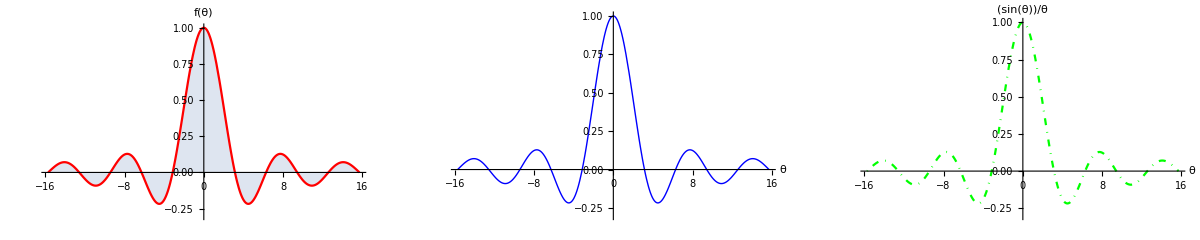

```mathematica
GraphicsRow[{
Plot[Style[f[θ], Red],{θ, -5 π, 5 π}, PlotRange->{-0.3, 1}, PlotLabel-> "f(θ)", Filling->Axis], 
Plot[Style[f[θ], Blue, Thick],{θ, -5 π, 5 π}, PlotRange->{-0.3, 1}, AxesLabel -> Automatic], 
Plot[Style[f[θ], Green, DotDashed],{θ, -5 π, 5 π}, PlotRange->{-0.3, 1}, AxesLabel-> {θ, f[θ]}]
}, ImageSize->Full, Frame->All] 
(* The row looks normal under wide-screen conditions due to scaling from `ImageSize -> Full` *)
```

## Problem 3

Area of square; x^2
Area of circle: π*r^2
But the material will be used for the circumference; C = 2πr
Relate to the perimeter of a square... 
2πr + 4x = 10
2πr = 10 - 4x
r = (5-2x)/π or r = 1/π(5-2x)
So the total area = π r^2 + x^2
Substituting r^2 , this gives: A_T = 1/π(5-2x)^2 + x^2

```mathematica
Clear[f] (* Clear old function *)
```

A.

```mathematica
f[x_] = 1/π(5-2x)^2 + x^2 (* = Total area *)
```

(5-2 x)^2/π+x^2

Plot the graphs for a better look at their behaviors.

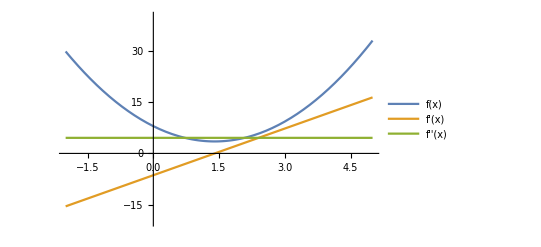

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -2, 5}, PlotRange->{-20, 40}, PlotLegends->Placed["Expressions", {0.40, 0.85}], PlotStyle->Automatic]
```

B.
As one might expect from the function, the graph is in the shape of a parabola, meaning that there will only be one root.

```mathematica
Solve[f'[x] == 0, x] (* Solve for critical point -- where the derivative of the area function == 0 *)
```

{{x→10/(4+π)}}

```mathematica
NSolve[f'[x] == 0, x] (* Decimal answer *)
```

{{x→1.40025}}

C.
This point is a global minimum, as it is the lowest point on the parabola. Which also means that this is the smallest possible area one could make.

D.
Since this is a concave-up parabola, the global maximum of f(x) is ∞ at x = ±∞
(I initially tried FindMaximum as well, but it couldn’t find ∞. Which makes a lot of sense.)

E.
Since this problem only exists for 0 ≤ x ≤ 10 units, (or 0 ≤ x ≤ 2.5 if it’s 100% a square -> 4 sides), then the maximum area that can be made is to not cut the wire at all and use all 10 units to make the circle.
After some rearranging, this would give...

```mathematica
AreaFromCirc[c_] = 1/(4π)c^2 (* From solving circumference for r and substituting into area formula. *)
```

c^2/(4 π)

```mathematica
AreaFromCirc[10]
```

25/π

So 25/π is the largest area that can be made.